```mathematica
$AllowedBAC= 0.08;
```

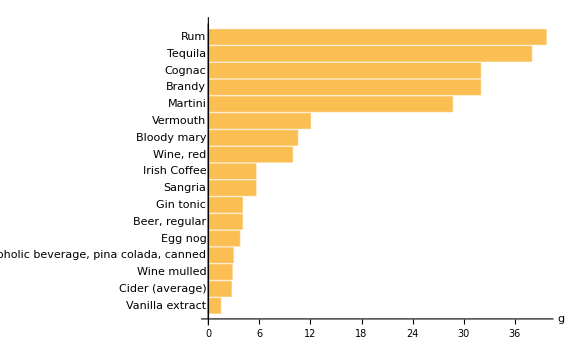

```mathematica
alcoholicDrinks={Entity["Food","Martini::c6h98"],Entity["Food","VanillaExtract::6g22f"],Entity["Food","BloodyMary::328gx"],Entity["Food","Brandy::q5447"],Entity["Food","Vermouth::679s2"],Entity["Food","Cognac::y9462"],Entity["Food","BeerRegular::8x3f9"], Entity["Food","EggNog::3dwyy"],Entity["Food","WineMulled::2t398"],Entity["Food","CiderAverage::5dtvm"],Entity["Food","GinTonic::n5779"],Entity["Food","Sangria::xmm5b"],Entity["Food","Rum::889s3"],Entity["Food","Tequila::nb2x5"],Entity["Food","AlcoholicBeveragePinaColadaCanned::vv7h8"],Entity["Food","IrishCoffee::6pv9d"],Entity["Food","WineRed::qxm3p"]};
alcoholicContent = EntityValue[alcoholicDrinks,"AlcoholContentPerServing","EntityAssociation"];
BarChart[Sort[alcoholicContent], ChartLabels->Automatic,AxesLabel->Automatic, BarOrigin-> Left, ImageSize->Large]
```

```mathematica
alcoholConsumed[drinktype_,numberofdrinks_]:=Quantity[QuantityMagnitude@EntityValue[drinktype,"AlcoholContentPerServing"]*numberofdrinks*0.035274,"Ounces"]

calculateBAC[bodyweight_,drinktype_, numberofdrinks_,sex_,timepassed_]:= (QuantityMagnitude@alcoholConsumed[drinktype,numberofdrinks]*5.14/(bodyweight * If[SameQ[sex,"male"],0.73,0.66]))-(0.015*timepassed)
(*bodyweight in pounds, alcohol consumed in ounces, sex either "male" or anything, timepassed in hours*)

(*write it like a story? ends with should you drive and if not how long should you wait to drive*)

(* for a generic person *)
bodyweight = 100;
drinktype = Entity["Food","Martini::c6h98"];
numberofdrinks=1;
sex = male;
timepassed = 1;

BAC= calculateBAC[bodyweight,drinktype, numberofdrinks,sex,timepassed];

canIDriveQ[bac_]:= If[bac≤ $AllowedBAC, "Yes","No"];

BACvisual[bac_]:= PieChart[{bac, 1-bac}, ChartLabels->{alcohol, blood}];

canIDriveQ
BACvisual
```

Yes

-Graphics-

Recently, I visited the United Kingdom, which is where the inspiration for this essay comes from. Boy do people drink there! I was at a very famous pub in Oxford, called Turf Tavern, and I witnessed an interesting conversation. Two gentlemen were talking about getting home. “I can drive in a little bit when I’ve sobered up!” and that got me thinking, exactly how long would it take that particular gentleman to “sober up” enough to be able to drive safely. I decided to create this for anyone to decide how long it would take. People at bars generally don’t know the exact amount of alcohol they have consumed.